# Les valeurs propres et les vecteurs propres de l’opérateurs Hermitien (Opérateur matriciel)

## Initiation

### Définition du produit scalaire

```mathematica
⟨x_|y_⟩:=∑_(i=1)^Length[x] x⟦i⟧*y⟦i⟧
```

### Constante de Planck

```mathematica
ℏ=1;
```

```mathematica
(*ℏ=1.054571726×10^(−34);*)
```

## Quelques Opérateurs Hermitien

### Opérateurs Spin

Les matrices de Pauli:

```mathematica
Subscript[σ, x]=({{0, 1}, {1, 0}});
```

```mathematica
Subscript[σ, y]=({{0, -ⅈ}, {ⅈ, 0}});
```

```mathematica
Subscript[σ, z]=({{1, 0}, {0, -1}});
```

```mathematica
Subscript[S, x]=ℏ/2 Subscript[σ, x];Subscript[S, y]=ℏ/2 Subscript[σ, y];Subscript[S, z]=ℏ/2 Subscript[σ, z];
```

```mathematica
Subscript[S, x]//MatrixForm
```

(0 | 1/2
1/2 | 0)

```mathematica
Subscript[S, y]//MatrixForm
```

(0 | -ⅈ/2
ⅈ/2 | 0)

```mathematica
Subscript[S, z]//MatrixForm
```

(1/2 | 0
0 | -1/2)

```mathematica
Subscript[J, x]=({{0, ℏ/(√2), 0}, {ℏ/(√2), 0, ℏ/(√2)}, {0, ℏ/(√2), 0}});
```

```mathematica
Subscript[J, y]=({{0, -(ⅈ ℏ)/(√2), 0}, {(ⅈ ℏ)/(√2), 0, -(ⅈ ℏ)/(√2)}, {0, (ⅈ ℏ)/(√2), 0}});
```

```mathematica
Subscript[J, z]=({{ℏ, 0, 0}, {0, 0, 0}, {0, 0, -ℏ}});
```

```mathematica
J2=({{2 ℏ^2, 0, 0}, {0, 2 ℏ^2, 0}, {0, 0, 2 ℏ^2}});
```

## Opérateur auto-adjoint (Hermitienne) Â

```mathematica
Â:=Subscript[S, z]
```

```mathematica
dim:=Length[Â]
```

### Opérateur adjoint (conjugué Hermitique )

```mathematica
ConjugateTranspose[Â]//MatrixForm
```

(1/2 | 0
0 | -1/2)

### Est ce que l’operateur Â est auto - adjoint?

```mathematica
ConjugateTranspose[Â]==Â
```

True

## Les valeurs propres de l’operateur Â

```mathematica
a=Eigenvalues[Â]
```

{-1/2,1/2}

```mathematica
Subscript[a, n_]:=a[[n]]
```

### Est ce que les valeurs propres de l’operateur Â sont réel ?

```mathematica
a* == a
```

True

## Les vecteures (états) propres de l’operateur Â

```mathematica
u=Eigenvectors[Â]
```

{{0,1},{1,0}}

```mathematica
Subscript[u, n_]:=u[[n]]
```

```mathematica
Table[⟨Subscript[u, m]|Subscript[u, n]⟩,{m,1,dim},{n,1,dim}]//TableForm
```

1 | 0
0 | 1

### Est ce que les vecteurs propres de l’operateur Â sont orthogonaux ?

```mathematica
Orthogonalize[Table[⟨Subscript[u, m]|Subscript[u, n]⟩,{m,1,dim},{n,1,dim}]]==IdentityMatrix[dim]
```

True

```mathematica
Grid[Table[{Subscript[a, n],Subscript[u, n]//MatrixForm},{n,1,dim}]]
```

-1/2 | (0
1)
1/2 | (1
0)

```mathematica
Grid[Transpose[
Eigensystem[Â]
],Dividers->All]
```

-1/2 | {0,1}
1/2 | {1,0}

## Normaliser de la base des fonctions propres de l’opérateur Â

```mathematica
Subscript[ϕ, n_]:=Subscript[u, n]/(√⟨Subscript[u, n]|Subscript[u, n]⟩)
```

```mathematica
Table[Subscript[ϕ, n],{n,1,dim}]//Simplify
```

{{0,1},{1,0}}

```mathematica
Table[⟨Subscript[ϕ, m]|Subscript[ϕ, n]⟩,{m,1,dim},{n,1,dim}]//TableForm
```

1 | 0
0 | 1

## Décomposer un état quantique quelconque en une combinaison linéaire d’états propres

Soit un système dans un état quantique décrit par un vecteur arbitraire normalisé :

```mathematica
ψ=Normalize[∑_(n=1)^dim RandomInteger[{-5,5}] Subscript[u, n]]
```

{3/(√10),1/(√10)}

### Les coéfficients

```mathematica
Subscript[C, n_]:=⟨Subscript[ϕ, n]|ψ ⟩
```

```mathematica
Table[{n,Subscript[C, n]},{n,1,dim}]//Simplify//TableForm
```

1 | 1/(√10)
2 | 3/(√10)

### Développement de ψ sur ϕ_n

```mathematica
∑_(n=1)^dim Subscript[C, n] Subscript["ϕ", n]//N
```

0.316228 ϕ_1+0.948683 ϕ_2

## La probabilité de trouver a_n (non-dégénérée) dans la mesure de l’operateur Â

P[n] donne la probabilité pour qu' un état propre ψ_n avec la valeur propre a_n soit le résultat de la mesure d' un état quantique ψ :

```mathematica
P[n_]:=Abs[Subscript[C, n]]^2
```

```mathematica
Table[{n,N[P[n],2]},{n,1,dim}]//TableForm
```

1 | 0.1
2 | 0.9

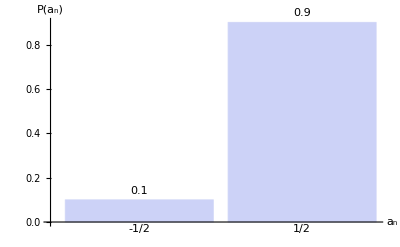

```mathematica
BarChart[Table[N[P[n],2],{n,dim}],LabelingFunction->Above,AxesLabel->{"a_n","P(a_n)"},ChartLabels->a]
```

```mathematica
∑_(n=1)^dim P[n]//N
```

1.

## Valeur moyenne de l’operateur Â (espérance quantique)

### Définition

La valeur moyenne de Â dans un état pur,décrit par un vecteur normalisé ψ :

```mathematica
⟨x_|A_|x_⟩:=⟨x|⟨A|x⟩⟩//FullSimplify
```

```mathematica
⟨Â⟩=⟨ψ|Â|ψ⟩
```

2/5

```mathematica
⟨ψ|Â|ψ⟩==⟨ψ|Â|ψ⟩*==⟨ψ|Â†|ψ⟩
```

True

```mathematica
⟨(Â)^2⟩=⟨ψ|(Â)^2|ψ⟩
```

1/4

## Écart quadratique moyen de l’operateur Â

```mathematica
ΔA=√(⟨ψ|(Â)^2|ψ⟩-⟨ψ|Â|ψ⟩^2)//N
```

0.3